# Exact solution for the motion of spinning particles near spherically symmetric compact objects

In this notebook we go through the computations presented in the paper “Exact solutions for the motion of spinning particles near spherically symmetric black holes and exotic compact objects” by Vojtěch Witzany and Gabriel Andres Piovano. The reader should be able to in principle follow almost every step of the computation from the paper by examining this notebook. There is one step for which Maple was better suited (expression of quadratures in terms of Jacobi elliptic integrals), which can be found in an additional Maple notebook. This notebook was written by Vojtěch Witzany and Gabriel Andres Piovano.

## Setting up Static, spherically symmetric metric

### Christoffel, Riemann for any space-time

```mathematica
InverseMetric[g_]:=Simplify[Inverse[g]]
(*First index up, second two down:*)
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=4;ig=InverseMetric[g];
res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];
Simplify[res]]
(*First index up, rest down:*)
RiemannTensor[g_,xx_]:=Block[{n,Chr,res},n=4;Chr=ChristoffelSymbol[g,xx];
res=Table[D[Chr[[i,k,m]],xx[[l]]]-D[Chr[[i,k,l]],xx[[m]]]+Sum[Chr[[i,s,l]]*Chr[[s,k,m]],{s,1,n}]-Sum[Chr[[i,s,m]]*Chr[[s,k,l]],{s,1,n}],{i,1,n},{k,1,n},{l,1,n},{m,1,n}];
Simplify[res]]
(*Two lower indices:*)
RicciTensor[g_,xx_]:=Block[{Rie,res,n},n=4;Rie=RiemannTensor[g,xx];
res=Table[Sum[Rie[[s,i,s,j]],{s,1,n}],{i,1,n},{j,1,n}];
Simplify[res]]
RicciScalar[g_,xx_]:=Block[{Ricc,ig,res,n},n=4;Ricc=RicciTensor[g,xx];ig=InverseMetric[g];
res=Sum[ig[[s,i]] Ricc[[s,i]],{s,1,n},{i,1,n}];
Simplify[res]]
```

### Specializing to static, spherically symmetric metric

```mathematica
gtt = -f[r];
grr= h[r];
fhRule = {f->(1-2M/#&),h ->(1/(1-2M/#)& )}; (*In case you want to substitute Schwarzschild*)
gθθ= r^2 ;
gϕϕ= r^2 Sin[θ]^2;
xx={t,ϕ,r,θ};
g={{gtt,0,0,0},{0,gϕϕ,0,0},{0,0,grr,0},{0,0,0,gθθ}};
ig = InverseMetric[g];
sqrtg = Simplify[Sqrt[-Det[g]],{r>0,0<θ<π}];
ChrisSchw=ChristoffelSymbol[g,xx];
RiemSchw = RiemannTensor[g,xx];
(*All lower indices*)
Riemd = Table[Sum[RiemSchw[[s,j,k,l]]g[[i,s]],{s,1,4}],{i,1,4},{j,1,4},{k,1,4},{l,1,4}];
```

## Killing vectors

### Killing vectors with indices up

```mathematica
xit = {1,0,0,0};
xix = {0,-Cos[ϕ]Cot[θ],0,-Sin[ϕ]};
xiy = { 0,-Sin[ϕ]Cot[θ],0,Cos[ϕ]};
xiz = {0,1,0,0};
```

### Lie derivative of metric by xi

```mathematica
Lxig[xi_] := Module[{xid},
xid = Table[Sum[xi[[i]]g[[i,j]],{i,1,4}],{j,1,4}];
Simplify[Table[D[xid[[j]],xx[[k]]]+D[xid[[k]],xx[[j]]] - 2Sum[ChrisSchw[[i,j,k]]xid[[i]],{i,1,4}],{j,1,4},{k,1,4}]]
]
ximunu[xi_] := Module[{xid},
xid = Table[Sum[xi[[i]]g[[i,j]],{i,1,4}],{j,1,4}];
1/2 Simplify[Table[D[xid[[j]],xx[[k]]]- D[xid[[k]],xx[[j]]],{j,1,4},{k,1,4}]]
]
```

### Verifying Killing equation

```mathematica
Lxig[xit]
Lxig[xix]
Lxig[xiy]
Lxig[xiz]
ximunu[xit]
ximunu[xix]
ximunu[xiy]
ximunu[xiz]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

«1 more identical outputs»

{{0,0,-1/2 f'[r],0},{0,0,0,0},{f'[r]/2,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,-r Cos[θ] Cos[ϕ] Sin[θ],r^2 Cos[ϕ] Sin[θ]^2},{0,1/2 r Cos[ϕ] Sin[2 θ],0,r Sin[ϕ]},{0,-r^2 Cos[ϕ] Sin[θ]^2,-r Sin[ϕ],0}}

{{0,0,0,0},{0,0,-r Cos[θ] Sin[θ] Sin[ϕ],r^2 Sin[θ]^2 Sin[ϕ]},{0,1/2 r Sin[2 θ] Sin[ϕ],0,-r Cos[ϕ]},{0,-r^2 Sin[θ]^2 Sin[ϕ],r Cos[ϕ],0}}

{{0,0,0,0},{0,0,r Sin[θ]^2,1/2 r^2 Sin[2 θ]},{0,-r Sin[θ]^2,0,0},{0,-r^2 Cos[θ] Sin[θ],0,0}}

## Dynamics of spinning particle

### Dynamical variables

```mathematica
xt = {tt[τ],ϕt[τ],rt[τ],θt[τ]};
TrRule = Table[xx[[i]]->xt[[i]],{i,1,4}]; (*Substitute trajectory into coordinate expressions*)
DeTrRule = Join[
Table[xt[[i]]->xx[[i]],{i,1,4}],
Table[D[xt[[i]],τ]->u^xx[[i]],{i,1,4}],
{St[τ]->s^t,Sr[τ]->s^r,Sϕ[τ]->s^ϕ,Sθ[τ]->s^θ}
];  (*Not useful but visually nice symbolic presentation*)
ucov = D[xt,τ]; (*Four-velocity, indices up*)
ucon = Table[Sum[ucov[[i]]g[[i,j]],{i,1,4}],{j,1,4}]; (*Four-velocity, indices down*)
```

### Spin vector and tensor

```mathematica
(*Svec is the spin vector and has indices up*)
Svec = ϵ{St[τ],Sϕ[τ],Sr[τ],Sθ[τ]};
(*Spin tensor in terms of spin vector, indices up*)
Stens = Simplify[Table[1/sqrtg Sum[LeviCivitaTensor[4][[i,j,k,l]]ucon[[k]]g[[l,m]]Svec[[m]],{k,1,4},{l,1,4},{m,1,4}],{i,1,4},{j,1,4}]];
(*Pretty representation of spin tensor:*)(Stens/.DeTrRule/.{ϵ->1})//Simplify//MatrixForm
```

(0 | ((s^θ u^r-s^r u^θ) Csc[θ] h[r])/(√(f[r] h[r])) | (r^2 (s^ϕ u^θ-s^θ u^ϕ) Sin[θ])/(√(f[r] h[r])) | ((-s^ϕ u^r+s^r u^ϕ) h[r] Sin[θ])/(√(f[r] h[r]))
((-s^θ u^r+s^r u^θ) Csc[θ] h[r])/(√(f[r] h[r])) | 0 | ((-s^θ u^t+s^t u^θ) Csc[θ] f[r])/(√(f[r] h[r])) | ((-s^t u^r+s^r u^t) Csc[θ] √(f[r] h[r]))/r^2
-(r^2 (s^ϕ u^θ-s^θ u^ϕ) Sin[θ])/(√(f[r] h[r])) | ((s^θ u^t-s^t u^θ) Csc[θ] f[r])/(√(f[r] h[r])) | 0 | ((-s^ϕ u^t+s^t u^ϕ) f[r] Sin[θ])/(√(f[r] h[r]))
((s^ϕ u^r-s^r u^ϕ) h[r] Sin[θ])/(√(f[r] h[r])) | ((s^t u^r-s^r u^t) Csc[θ] √(f[r] h[r]))/r^2 | ((s^ϕ u^t-s^t u^ϕ) f[r] Sin[θ])/(√(f[r] h[r])) | 0)

```mathematica
(*Consistency checks*)
```

```mathematica
suOnShell ={tt'[τ] -> √((-1-grr rt'[τ]^2-gϕϕ ϕt'[τ]^2 -gθθ θt'[τ]^2)/gtt),St[τ]-> √((-S^2-grr Sr[τ]^2-gϕϕ Sϕ[τ]^2 -gθθ Sθ[τ]^2)/gtt)};
Table[FullSimplify[ExpandAll[Sum[Stens[[i,j]]g[[j,l]]Svec[[l]]/.suOnShell,{j,1,4},{l,1,4}]]],{i,1,4}]
Table[FullSimplify[ExpandAll[Sum[Stens[[i,j]]ucon[[j]]/.suOnShell,{j,1,4},{l,1,4}]]],{i,1,4}]
```

{0,0,0,0}

{0,0,0,0}

### Equations of motion

```mathematica
(*Equations of motion in the form of substitutions/rules*)
xEOM = Table[D[ucov[[i]],τ]-> -Sum[ChrisSchw[[i,j,k]]ucov[[j]]ucov[[k]],{j,1,4},{k,1,4}]- 1/2 Sum[RiemSchw[[i,j,k,l]]ucov[[j]]Stens[[k,l]],{j,1,4},{k,1,4},{l,1,4}] ,{i,1,4}]/.TrRule;
SEOM = Table[D[Svec[[i]]/ϵ,τ]-> Simplify[-Sum[ChrisSchw[[i,j,k]] Svec[[j]]ucov[[k]],{j,1,4},{k,1,4}]/ϵ],{i,1,4}]/.TrRule;
```

## Constants of motion

### Killing constants of motion

```mathematica
SpConst[xi_]:= Sum[ucon[[i]]xi[[i]],{i,1,4}] - 1/2 Sum[D[Sum[xi[[k]]g[[i,k]],{k,1,4}],xx[[j]]]Stens[[i,j]],{i,1,4},{j,1,4}]
Es = -SpConst[xit]//FullSimplify[#,{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}]&
Jx = SpConst[xix]//FullSimplify[#,{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}]&
Jy = SpConst[xiy]//FullSimplify[#,{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}]&
Jz =SpConst[xiz]//FullSimplify[#,{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}]&
Jv = {Jx,Jy,Jz}//FullSimplify[#,{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}]&;
```

f[r] tt'[τ]+(r^2 ϵ Sin[θ] f'[r] (-Sϕ[τ] θt'[τ]+Sθ[τ] ϕt'[τ]))/(2 √(f[r] h[r]))

Sin[θ] (-r^2 (Csc[θ] Sin[ϕ] θt'[τ]+Cos[θ] Cos[ϕ] ϕt'[τ])+(ϵ f[r] (Cos[ϕ] h[r] (St[τ] rt'[τ]-Sr[τ] tt'[τ])+r (-Cos[ϕ] Cot[θ] Sθ[τ] tt'[τ]+Sin[ϕ] Sϕ[τ] tt'[τ]+Cos[ϕ] Cot[θ] St[τ] θt'[τ]-Sin[ϕ] St[τ] ϕt'[τ])))/(√(f[r] h[r])))

r^2 (Cos[ϕ] θt'[τ]-Cos[θ] Sin[θ] Sin[ϕ] ϕt'[τ])+(ϵ f[r] (Sin[ϕ] (h[r] Sin[θ] (St[τ] rt'[τ]-Sr[τ] tt'[τ])+r Cos[θ] (-Sθ[τ] tt'[τ]+St[τ] θt'[τ]))+r Cos[ϕ] Sin[θ] (-Sϕ[τ] tt'[τ]+St[τ] ϕt'[τ])))/(√(f[r] h[r]))

(ϵ f[r] (Cos[θ] h[r] (St[τ] rt'[τ]-Sr[τ] tt'[τ])+r Sin[θ] (Sθ[τ] tt'[τ]-St[τ] θt'[τ])))/(√(f[r] h[r]))+r^2 Sin[θ]^2 ϕt'[τ]

```mathematica
(*Verify that constants are conserved by EOM up to spin squared terms*)
Simplify[Series[D[Es/.TrRule,τ]/.xEOM/.SEOM/.TrRule,{ϵ,0,1}]]
Simplify[Series[D[Jx/.TrRule,τ]/.xEOM/.SEOM/.TrRule,{ϵ,0,1}]]
Simplify[Series[D[Jy/.TrRule,τ]/.xEOM/.SEOM/.TrRule,{ϵ,0,1}]]
Simplify[Series[D[Jz/.TrRule,τ]/.xEOM/.SEOM/.TrRule,{ϵ,0,1}]]
```

O[ϵ]^2

O[ϵ]^2

O[ϵ]^2

«1 more identical outputs»

### Angular - momentum vector l^μ and s_(||)

```mathematica
(*An additional constant is associated with the angular-momentum vector l*)
l = rt[τ]{0,-θt'[τ]/Sin[θt[τ]],0,Sin[θt[τ]]ϕt'[τ]};
ug = {tt'[τ],ϕt'[τ],rt'[τ],θt'[τ]};
(*Verify parallel transport of l vector:*)
Table[(D[l[[i]],τ]+Sum[ChrisSchw[[i,j,k]]ug[[j]]l[[k]],{j,1,4},{k,1,4}])/.TrRule/.xEOM/.{ϵ->0}/.TrRule,{i,1,4}]//Simplify
```

{0,0,0,0}

```mathematica
(*The aligned component of spin, denoted by s_∥ in paper*)
spara =( (l.g.Svec)/(√(l.g.l)))/.TrRule//Simplify
(*Verify conservation of s_∥*)
Series[(D[spara,τ]/.xEOM/.SEOM/.TrRule),{ϵ,0,1}]//FullSimplify
```

(ϵ rt[τ]^3 Sin[θt[τ]] (-Sϕ[τ] θt'[τ]+Sθ[τ] ϕt'[τ]))/(√(rt[τ]^4 (θt'[τ]^2+Sin[θt[τ]]^2 ϕt'[τ]^2)))

O[ϵ]^2

## Rotating into aligned plane

### Alignment of general vector

```mathematica
(*Defining quantitities such as cos(ι), sin(ι), 𝒥,...*)
(*Note that the values of Subscript[𝒥, x] etc do not need to be substituted explicitly, since the formulas apply in general*)
ci = JJz/JJ;
si =√(1 - ci^2);
JJ = √(JJx^2+JJy^2+JJz^2);
n = 1/(JJ si){-JJy,JJx,0};
Align[v_]:=n(n.v) + ci(Cross[Cross[n,v],n]) - si(Cross[n,v]);
BackAlign[v_]:=n(n.v) + ci(Cross[Cross[n,v],n]) + si(Cross[n,v]);
```

```mathematica
(*Check that alignment works*)
Jalign = Align[{JJx,JJy,JJz}]//FullSimplify
(*Check that inverse transofrm works*)
BackAlign[Jalign]//FullSimplify
```

{0,0,√(JJx^2+JJy^2+JJz^2)}

{JJx,JJy,JJz}

### Transformation of spherical polar coordinates

```mathematica
(*Unit position vectors transformed there and back*)
{xp,yp,zp}=Align[{Sin[θ]Sin[ϕ],Sin[θ]Cos[ϕ],Cos[θ]}]//FullSimplify
{xh,yh,zh}=BackAlign[{Sin[ϑ]Sin[φ],Sin[ϑ]Cos[φ],Cos[ϑ]}]//FullSimplify
```

{(-JJx (JJx^2+JJy^2) Cos[θ]+Sin[θ] (JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Cos[ϕ]+(JJx^2 JJz+JJy^2 √(JJx^2+JJy^2+JJz^2)) Sin[ϕ]))/((JJx^2+JJy^2) √(JJx^2+JJy^2+JJz^2)),(-JJy (JJx^2+JJy^2) Cos[θ]+Sin[θ] ((JJy^2 JJz+JJx^2 √(JJx^2+JJy^2+JJz^2)) Cos[ϕ]+JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Sin[ϕ]))/((JJx^2+JJy^2) √(JJx^2+JJy^2+JJz^2)),(JJz Cos[θ]+Sin[θ] (JJy Cos[ϕ]+JJx Sin[ϕ]))/(√(JJx^2+JJy^2+JJz^2))}

{(JJx (JJx^2+JJy^2) Cos[ϑ]+Sin[ϑ] (JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Cos[φ]+(JJx^2 JJz+JJy^2 √(JJx^2+JJy^2+JJz^2)) Sin[φ]))/((JJx^2+JJy^2) √(JJx^2+JJy^2+JJz^2)),(JJy (JJx^2+JJy^2) Cos[ϑ]+Sin[ϑ] ((JJy^2 JJz+JJx^2 √(JJx^2+JJy^2+JJz^2)) Cos[φ]+JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Sin[φ]))/((JJx^2+JJy^2) √(JJx^2+JJy^2+JJz^2)),(JJz Cos[ϑ]-Sin[ϑ] (JJy Cos[φ]+JJx Sin[φ]))/(√(JJx^2+JJy^2+JJz^2))}

```mathematica
(*Forward transform*)
(*cos(ϑ):*)
zp
(*tan(φ):*)
xp/yp//FullSimplify
```

(JJz Cos[θ]+Sin[θ] (JJy Cos[ϕ]+JJx Sin[ϕ]))/(√(JJx^2+JJy^2+JJz^2))

(-JJx (JJx^2+JJy^2) Cos[θ]+Sin[θ] (JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Cos[ϕ]+(JJx^2 JJz+JJy^2 √(JJx^2+JJy^2+JJz^2)) Sin[ϕ]))/(-JJy (JJx^2+JJy^2) Cos[θ]+Sin[θ] ((JJy^2 JJz+JJx^2 √(JJx^2+JJy^2+JJz^2)) Cos[ϕ]+JJx JJy (JJz-√(JJx^2+JJy^2+JJz^2)) Sin[ϕ]))

```mathematica
(*Inverse transform*)
(*cos(θ):*)
cθ=(zh/.{JJx -> Sin[ξ]Sin[ι],JJy ->Cos[ξ]Sin[ι],JJz -> Cos[ι]})//FullSimplify//TrigReduce//FullSimplify//TrigReduce//FullSimplify
(*tan(ϕ):*)
tϕ = (xh/yh/.{JJx -> Sin[ξ]Sin[ι],JJy ->Cos[ξ]Sin[ι],JJz -> Cos[ι]})//FullSimplify//TrigReduce//Simplify//TrigReduce//FullSimplify//ExpandAll//FullSimplify
```

Cos[ϑ] Cos[ι]-Cos[ξ-φ] Sin[ϑ] Sin[ι]

(2 (Cos[ι] Cos[ξ-φ] Sin[ϑ]+Cos[ϑ] Sin[ι]) Sin[ξ]-2 Cos[ξ] Sin[ϑ] Sin[ξ-φ])/(((-1+Cos[ι]) Cos[2 ξ-φ]+2 Cos[ι/2]^2 Cos[φ]) Sin[ϑ]+2 Cos[ϑ] Cos[ξ] Sin[ι])

```mathematica
Series[ArcCos[cθ]/.{ϑ->π/2+δϑ},{δϑ,0,1}]//FullSimplify
Series[ArcTan[tϕ//TrigReduce]/.{ϑ->π/2+δϑ},{δϑ,0,1}]//FullSimplify
```

(π-ArcCos[Cos[ξ-φ] Sin[ι]])+(Cos[ι] δϑ)/(√(1-Cos[ξ-φ]^2 Sin[ι]^2))+O[δϑ]^2

ArcTan[(-Sin[ι/2]^2 Sin[2 ξ-φ]+Cos[ι/2]^2 Sin[φ])/(Cos[ι/2]^2 Cos[φ]-Cos[2 ξ-φ] Sin[ι/2]^2)]-(4 (Sin[ι] Sin[ξ-φ]) δϑ)/(3+Cos[2 ι]-2 Cos[2 (ξ-φ)] Sin[ι]^2)+O[δϑ]^2

```mathematica
(*More elegant expression for tan(ϕ):*)
```

```mathematica
tϕ - ((Cos[ϑ]Sin[ι]Sin[ξ] + Sin[ϑ](Cos[ι/2]^2 Sin[φ] - Sin[ι/2]^2 Sin[2ξ - φ]))/(Cos[ϑ]Sin[ι]Cos[ξ] + Sin[ϑ](Cos[ι/2]^2 Cos[φ] - Sin[ι/2]^2 Cos[2ξ - φ])))//FullSimplify
```

0

## Solving for motion in aligned coordinates

### Solving for ϑ in aligned coordinates

```mathematica
(*Now the constraints following from rotating the coordinate system into J*)
Series[Jx/.{θ->θt[τ]}/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//Simplify
Series[Jy/.{θ->θt[τ]}/.{θt->(π/2+ϵ δθt[#]&)},{ϵ,0,1}]//Simplify
```

(r^2 (-Sin[ϕ] δθt'[τ]+Cos[ϕ] δθt[τ] ϕt'[τ])+(f[r] (Cos[ϕ] h[r] (St[τ] rt'[τ]-Sr[τ] tt'[τ])+r Sin[ϕ] (Sϕ[τ] tt'[τ]-St[τ] ϕt'[τ])))/(√(f[r] h[r]))) ϵ+O[ϵ]^2

(r^2 (Cos[ϕ] δθt'[τ]+Sin[ϕ] δθt[τ] ϕt'[τ])+(f[r] (h[r] Sin[ϕ] (St[τ] rt'[τ]-Sr[τ] tt'[τ])+r Cos[ϕ] (-Sϕ[τ] tt'[τ]+St[τ] ϕt'[τ])))/(√(f[r] h[r]))) ϵ+O[ϵ]^2

```mathematica
(*The two expressions below vanish independently*)
k1 = Coefficient[Series[Jx/.{θ->θt[τ]}/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//Simplify,ϵ Cos[ϕ]]
k2 = FullSimplify[Coefficient[Series[Jx/.{θ->θt[τ]}/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//Simplify,ϵ Sin[ϕ]]]
```

(f[r] h[r] (St[τ] rt'[τ]-Sr[τ] tt'[τ]))/(√(f[r] h[r]))+r^2 δθt[τ] ϕt'[τ]

r (-r δθt'[τ]+(f[r] (Sϕ[τ] tt'[τ]-St[τ] ϕt'[τ]))/(√(f[r] h[r])))

```mathematica
(*One expression gives a constraint for δθt, another one for δθt'. Are they self-consistent?*)
Solve[k1 ==0,δθt[τ]]//Simplify
```

{{δθt[τ]→(√(f[r] h[r]) (-St[τ] rt'[τ]+Sr[τ] tt'[τ]))/(r^2 ϕt'[τ])}}

```mathematica
((D[(√(f[r] h[r]) (-St[τ] rt'[τ]+Sr[τ] tt'[τ]))/(r^2 ϕt'[τ])/.TrRule,τ]//Simplify/.xEOM/.SEOM)/.{ϵ->0}/.SEOM/.xEOM/.{θt->(π/2 + ϵ δθt[#]&)}/.{ϵ->0}/.TrRule//Simplify)/.TrRule/.{θt->(π/2 &)}//Simplify
```

(f[rt[τ]] (Sϕ[τ] tt'[τ]-St[τ] ϕt'[τ]))/(√(f[rt[τ]] h[rt[τ]]) rt[τ])

```mathematica
(*The first identity for δθt[τ] implies the vanishing of the second identity involving δθt'[τ]*)
1/2 r (-r δθt'[τ]+(f[r] (Sϕ[τ] tt'[τ]-St[τ] ϕt'[τ]))/(√(f[r] h[r])))/.TrRule/.{δθt'[τ]->(f[rt[τ]] (Sϕ[τ] tt'[τ]-St[τ] ϕt'[τ]))/(√(f[rt[τ]] h[rt[τ]]) rt[τ])}//Simplify
```

0

### Solving for r,t,φ in aligned coordinates

```mathematica
(*The remaining constants of motion have no dependence on theta at given order*)
Series[Es/.TrRule/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}](*/.fhRule/.{Sθ[τ]-> sp/rt[τ]}*)
Series[Jz/.TrRule/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]
Series[spara/.TrRule/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//FullSimplify[#,{ϕt'[τ]>0,rt[τ]>0}]&(*/.fhRule/.{Sθ[τ]-> sp/rt[τ]}*)
```

f[rt[τ]] tt'[τ]+(rt[τ]^2 Sθ[τ] f'[rt[τ]] ϕt'[τ] ϵ)/(2 √(f[rt[τ]] h[rt[τ]]))+O[ϵ]^2

rt[τ]^2 ϕt'[τ]+(f[rt[τ]] rt[τ] Sθ[τ] tt'[τ] ϵ)/(√(f[rt[τ]] h[rt[τ]]))+O[ϵ]^2

rt[τ] Sθ[τ] ϵ+O[ϵ]^2

```mathematica
(*Perturbative inversion to obtain time and phi components of four-velocity*)
utint = 1/f[rt[τ]](ℰ - ((rt[τ]^2 Sθ[τ] f'[rt[τ]] ϕt'[τ]) ϵ)/(2 √(f[rt[τ]] h[rt[τ]])))/.{ϕt'[τ]->𝒥/rt[τ]^2,Sθ[τ]->sp/rt[τ]}//Simplify;
uφint = 1/rt[τ]^2(𝒥 -(f[rt[τ]] rt[τ] Sθ[τ] tt'[τ] ϵ)/(√(f[rt[τ]] h[rt[τ]])))/.{tt'[τ]->ℰ/f[rt[τ]],Sθ[τ]->sp/rt[τ]}//Simplify;
tφRule = {tt'[τ]->utint,ϕt'[τ]->uφint};
urint2 = Series[(-1 - gtt utint^2 - gϕϕ uφint^2)/grr/.TrRule/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//Simplify//Normal
URule = {tt'[τ]->utint,ϕt'[τ]->uφint,rt'[τ]->Sqrt[urint2]}
```

(-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2)/h[rt[τ]]+(sp ℰ 𝒥 ϵ (2 f[rt[τ]]-rt[τ] f'[rt[τ]]))/((f[rt[τ]] h[rt[τ]])^(3/2) rt[τ]^2)

{tt'[τ]→(ℰ-(sp 𝒥 ϵ f'[rt[τ]])/(2 √(f[rt[τ]] h[rt[τ]]) rt[τ]))/f[rt[τ]],ϕt'[τ]→(𝒥-(sp ℰ ϵ)/(√(f[rt[τ]] h[rt[τ]])))/rt[τ]^2,rt'[τ]→√((-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2)/h[rt[τ]]+(sp ℰ 𝒥 ϵ (2 f[rt[τ]]-rt[τ] f'[rt[τ]]))/((f[rt[τ]] h[rt[τ]])^(3/2) rt[τ]^2))}

### Parallel transport in Marck-like tetrad

```mathematica
(*The spin vector fulfills non-trivial parallel-transport equations*)
Series[D[Svec,τ]/.SEOM/.TrRule/.{θt->(π/2 + ϵ δθt[#]&)},{ϵ,0,1}]//FullSimplify
```

{-((f'[rt[τ]] (St[τ] rt'[τ]+Sr[τ] tt'[τ])) ϵ)/(2 f[rt[τ]])+O[ϵ]^2,-((Sϕ[τ] rt'[τ]+Sr[τ] ϕt'[τ]) ϵ)/rt[τ]+O[ϵ]^2,-((Sr[τ] h'[rt[τ]] rt'[τ]+St[τ] f'[rt[τ]] tt'[τ]-2 rt[τ] Sϕ[τ] ϕt'[τ]) ϵ)/(2 h[rt[τ]])+O[ϵ]^2,-(Sθ[τ] rt'[τ] ϵ)/rt[τ]+O[ϵ]^2}

```mathematica
(*A Marck-like tetrad e0,er,eϕ,eθ (with indices up) allows to simplify parallel transport*)
LeadURule = {tt'[τ]->ℰ/f[rt[τ]],ϕt'[τ]->𝒥/rt[τ]^2,rt'[τ]->√((-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2)/h[rt[τ]])};
eθ = {0,0,0,1/r}/.TrRule
e0 = {tt'[τ],ϕt'[τ],rt'[τ],0}/.LeadURule/.TrRule
(*Note the component order t,φ,t,θ.*)
 
(*These are denoted as Subscript[ẽ, r],Subscript[ẽ, φ] in the paper: *)
ersol = FullSimplify[Solve[{(etr^2 gtt + err^2 grr/.TrRule/.{θt->(π/2 &)} )== 1,(etr e0[[1]]gtt + err e0[[3]]grr/.TrRule/.{θt->(π/2 &)}) ==0},{etr,err}],{rt[τ]>0,f[rt[τ]]>0, h[rt[τ]]>0}];
er = {etr,0,err,0}/.ersol[[2]]
eϕsol = FullSimplify[Solve[{(*(etϕ^2 gtt + eϕϕ^2 grr+ erϕ^2 grr/.TrRule/.{θt->(π/2 &)} )== 1,*)(etϕ e0[[1]]gtt+1 e0[[2]]gϕϕ + erϕ e0[[3]]grr/.TrRule/.{θt->(π/2 &)}) ==0,(etϕ er[[1]]gtt+1 er[[2]]gϕϕ + erϕ er[[3]]grr/.TrRule/.{θt->(π/2 &)}) ==0},{etϕ,(*eϕϕ,*)erϕ}],{rt[τ]>0,f[rt[τ]]>0, h[rt[τ]]>0,𝒥^2+rt[τ]^2>0}];
Nϕ = {etϕ ,1,erϕ,0}/.eϕsol[[1]];
eϕ =( Nϕ/Sqrt[Sum[Nϕ[[i]]Nϕ[[j]]g[[i,j]]/.TrRule/.{θt->(π/2 &)},{i,1,4},{j,1,4}]])//FullSimplify[#,{rt[τ]>0,f[rt[τ]]>0, h[rt[τ]]>0,𝒥^2+rt[τ]^2>0}]&
(*These reduce to the legs of the Marck tetrad in Schwarzschild*)
```

{0,0,0,1/rt[τ]}

{ℰ/f[rt[τ]],𝒥/rt[τ]^2,√((-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2)/h[rt[τ]]),0}

{(√(-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2) rt[τ])/(√(f[rt[τ]] (𝒥^2+rt[τ]^2))),0,(ℰ rt[τ])/(√(f[rt[τ]] h[rt[τ]] (𝒥^2+rt[τ]^2))),0}

{(ℰ 𝒥)/(f[rt[τ]] √(𝒥^2+rt[τ]^2)),(√(𝒥^2+rt[τ]^2))/rt[τ]^2,(𝒥 √((-1+(ℰ^2 rt[τ]^2)/(f[rt[τ]] (𝒥^2+rt[τ]^2)))/h[rt[τ]]))/rt[τ],0}

```mathematica
(*Sanity check: is tetrad orthonormal?*)
Emat = {e0,eϕ,er,eθ};
FullSimplify[Table[Sum[Emat[[i,j]]Emat[[k,l]]g[[j,l]]/.{θ->π/2}/.TrRule,{j,1,4},{l,1,4}],{i,1,4},{k,1,4}],{rt[τ]>0,f[rt[τ]]>0, h[rt[τ]]>0,𝒥^2+rt[τ]^2>0}]
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Similarly to Marck, we define a parallel-transported tetrad using the just defined legs*)
erder = FullSimplify[Table[(D[er[[i]],τ]+Sum[ChrisSchw[[i,j,k]]er[[j]]e0[[k]],{j,1,4},{k,1,4}])/.{θ->π/2}/.TrRule/.LeadURule,{i,1,4}],{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0}];
ψdot = FullSimplify[Sum[erder[[i]]eϕ[[l]]g[[i,l]]/.{θ->π/2}/.TrRule,{i,1,4},{l,1,4}],{f[rt[τ]]>0,h[rt[τ]]>0,rt[τ]>0,ℰ>0,𝒥^2+rt[τ]^2>0}]
ψdot/.fhRule//FullSimplify[#,{rt[τ]>2M>0,ℰ>0,𝒥^2+rt[τ]^2>0}]&
```

(ℰ 𝒥)/(√(f[rt[τ]] h[rt[τ]]) (𝒥^2+rt[τ]^2))

(ℰ 𝒥)/(𝒥^2+rt[τ]^2)

```mathematica
(*The parallel-transported spin vector can than be expressed through this tetrad as*)
SvecSol = FullSimplify[sp eθ + √(s^2-sp^2)(Sin[ψ]er + Cos[ψ]eϕ)]
```

{√((s-sp) (s+sp)) ((ℰ 𝒥 Cos[ψ])/(f[rt[τ]] √(𝒥^2+rt[τ]^2))+(√(-1+ℰ^2/f[rt[τ]]-𝒥^2/rt[τ]^2) rt[τ] Sin[ψ])/(√(f[rt[τ]] (𝒥^2+rt[τ]^2)))),(√((s-sp) (s+sp)) Cos[ψ] √(𝒥^2+rt[τ]^2))/rt[τ]^2,√((s-sp) (s+sp)) ((𝒥 Cos[ψ] √((-1+(ℰ^2 rt[τ]^2)/(f[rt[τ]] (𝒥^2+rt[τ]^2)))/h[rt[τ]]))/rt[τ]+(ℰ rt[τ] Sin[ψ])/(√(f[rt[τ]] h[rt[τ]] (𝒥^2+rt[τ]^2)))),sp/rt[τ]}

```mathematica
(*With the use of the precession angle we can now elegantly reexpress δϑ*)
((√(f[r] h[r]) (-St[τ] rt'[τ]+Sr[τ] tt'[τ]))/(r^2 ϕt'[τ]))/.TrRule/.LeadURule/.{St[τ]->SvecSol[[1]] ,Sr[τ]->SvecSol[[3]]}//FullSimplify[#,{rt[τ]>0,ℰ>0,𝒥^2+rt[τ]^2>0,f[rt[τ]]>0,h[rt[τ]]>0}]&
```

(√((s-sp) (s+sp) (𝒥^2+rt[τ]^2)) Sin[ψ])/(𝒥 rt[τ])

## Schwarzschild p,e parametrization

### The R(r;ℰ,𝒥,s_(||)) polynomial

```mathematica
(*Omitting the 1/r^3, ℛ is a cubic in Schwarzschild*)
Rpol = rt[τ]^4 urint2/.{Sθ[τ]->sp/rt[τ]}/.fhRule//Simplify
CoefficientList[Rpol,rt[τ]]//Simplify
Coefficient[Rpol,sp]/.{ϵ->1}
```

rt[τ] (2 M 𝒥 (𝒥-3 sp ℰ ϵ)-𝒥 (𝒥-2 sp ℰ ϵ) rt[τ]+2 M rt[τ]^2+(-1+ℰ^2) rt[τ]^3)

{0,2 M 𝒥 (𝒥-3 sp ℰ ϵ),-𝒥 (𝒥-2 sp ℰ ϵ),2 M,-1+ℰ^2}

rt[τ] (-6 M ℰ 𝒥+2 ℰ 𝒥 rt[τ])

### Corrections to ℰ and 𝒥 relation to eccentricity e and semi-latus rectum p

```mathematica
EJRule = {ℰ ->√(((p - 2M)^2 - 4M^2 e^2)/(p(p - M(3 + e^2)))+ϵ dE), 𝒥 -> √((M p^2)/(p - M(3 +e^2))+ϵ dJ)};
koef2 = Coefficient[Series[ExpandAll[Rpol]/.EJRule/.{rt[τ]->p/(1+e)},{ϵ,0,1}],ϵ];
koef1 =Coefficient[Series[ExpandAll[Rpol]/.EJRule/.{rt[τ]->p/(1-e)},{ϵ,0,1}],ϵ];
dEdJRule = Solve[{koef1==0,koef2==0},{dE,dJ}][[1]]//FullSimplify[#,{-((3+e^2) M)+p>0,p>0}]&
```

{dE→-((-1+e^2)^2 M^(3/2) √(p (-4 (-1+e^2) M^2-4 M p+p^2)) sp)/(p^2 (-((3+e^2) M)+p)^2),dJ→(√(M p) (-3 (3+e^2) M+2 p) √(-4 (-1+e^2) M^2-4 M p+p^2) sp)/((-((3+e^2) M)+p)^2)}

### Solving for third root r_3

```mathematica
(Solve[Coefficient[(1-ℰ^2)(r1 - r)(r-r2)(r-r3)(r-r4),r^2]==Coefficient[Rpol,rt[τ]^2],r3]/.{ℰ ->√(((p - 2M)^2 - 4M^2 e^2)/(p(p - M(3 + e^2)))+ϵ dE), 𝒥 -> √((M p^2)/(p - M(3 +e^2))+ϵ dJ)}/.{r1->p/(1-e),r2->p/(1+e),r4->0,ϵ->1}/.dEdJRule//Series[r3/.#,{sp,0,1}]&//Simplify)//FullSimplify[#,{-((3+e^2) M)+p>0,p>0,M>0}]&
```

{-(2 (M p))/(4 M-p)+((2 p √(M^3 p (-4 (-1+e^2) M^2-4 M p+p^2))-2 (3+e^2) √(M^5 p (-4 (-1+e^2) M^2-4 M p+p^2))) sp)/(M ((3+e^2) M-p) (-4 M+p)^2)+O[sp]^2}

```mathematica
(*Deriving a simpler expression for dr3*)
EQN = Series[Rpol/.EJRule/.dEdJRule /.{rt[τ]->r}/.{r->(2 M p)/(p-4M) + ϵ dr3},{ϵ,0,1}] //FullSimplify[#,{p>6M>0,0<e<1}]&//Coefficient[#,ϵ]&
```

-1/((-4 M+p)^4 (-((3+e^2) M)+p)^2)2 M^2 p^2 (dr3 (2 (3+e) M-p) ((3+e^2) M-p) (-4 M+p)^2 (2 (-3+e) M+p)+2 (-108 √(M^7 p (-4 (-1+e^2) M^2-4 M p+p^2))+4 e^4 √(M^7 p (-4 (-1+e^2) M^2-4 M p+p^2))+72 √(M^5 p^3 (-4 (-1+e^2) M^2-4 M p+p^2))-15 √(M^3 p^5 (-4 (-1+e^2) M^2-4 M p+p^2))+√(M p^7 (-4 (-1+e^2) M^2-4 M p+p^2))-e^2 (24 √(M^7 p (-4 (-1+e^2) M^2-4 M p+p^2))-8 √(M^5 p^3 (-4 (-1+e^2) M^2-4 M p+p^2))+√(M^3 p^5 (-4 (-1+e^2) M^2-4 M p+p^2)))) sp)

```mathematica
(dr3/.Solve[(EQN/.{M->1})==0,dr3][[1]])//FullSimplify[#,{p>0,0<e<1}]&
```

-(2 √((-4 e^2+(-2+p)^2) p) sp)/(-4+p)^2

```mathematica
rootsRule ={r1->p/(1-e),r2->p/(1+e),r3->(2 M p)/(p-4 M)-(2 √((-4 M^2 e^2+(-2M+p)^2) M p) sp)/(-4M+p)^2};
```

### The last stable orbits near p=(6+2e)M

```mathematica
Jac = {{D[ℰ/.EJRule/.dEdJRule,p],D[ℰ/.EJRule/.dEdJRule,e]},{D[𝒥/.EJRule/.dEdJRule,p],D[𝒥/.EJRule/.dEdJRule,e]}};
JacCoef =Coefficient[Series[Det[Jac]/.{p->(6+2e)M + sp dp,ϵ->1},{sp,0,1}]//FullSimplify//Normal,sp]
```

-(e (3+e) M^(5/2) (√2 dp e (-9+e^2) M^(3/2) √((1+e) M^2)+4 (-(1+e)^2 M^(3/2) √((3+e) M^2)+(-1+e)^2 √((1+e) M^2) √((1+e) (3+e) M^3))))/(4 (-3+e)^5 (1+e)^3 √(1/(9-e^2)) ((1+e) M^2)^(3/2) (-((3+e)^2 M^2)/((-3+e) (1+e)))^(3/2))

```mathematica
(*Now solve for the correction dp for LSO*)
Solve[JacCoef==0,dp]//FullSimplify[#,{0<e<1,M>0}]&
```

{{dp→-(2 √2 (1+e))/(√((1+e) (3+e)))}}

### Expressions for Mino velocities of t,ϕ DOF

```mathematica
(*Expressions for Mino velocities of t,ϕ DOF*)
CoefficientList[r^2utint/.fhRule/.{Sθ[τ]->sp/r,rt[τ]->r},ϵ]//FullSimplify
CoefficientList[r^2uφint/.fhRule/.{Sθ[τ]->sp/r,rt[τ]->r},ϵ]//FullSimplify
CoefficientList[r^2((ℰ 𝒥)/(𝒥^2+rt[τ]^2))/.fhRule/.{Sθ[τ]->sp/r,rt[τ]->r},ϵ]//FullSimplify
```

{-(r^3 ℰ)/(2 M-r),(M sp 𝒥)/(2 M-r)}

{𝒥,-sp ℰ}

{(r^2 ℰ 𝒥)/(r^2+𝒥^2)}

## Elliptic integrals and expansion

```mathematica
(*The elliptic integrals were computed in Maple, since it has better elliptic-integral algorithms.*) 
(*Here one can verify the results against numerical integrations.*)
```

### The λ(r) integrals, period, frequency

(p/(1-e)-r) r (-p/(1+e)+r) (-(2 p)/(-4+p)+r+(2 √((-4 e^2+(-2+p)^2) p) sp)/(-4+p)^2) (1-(-4 e^2+(-2+p)^2)/(p (-3-e^2+p))+((-1+e^2)^2 √(p (-4 (-1+e^2)-4 p+p^2)) sp)/(p^2 (-3-e^2+p)^2))

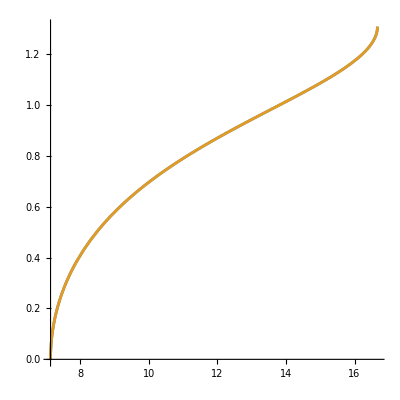

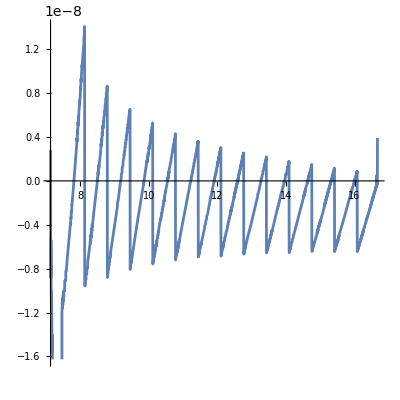

```mathematica
Subs = Join[EJRule/.dEdJRule/.{M->1,ϵ->1},rootsRule/.{M->1,ϵ->1},{M->1,ϵ->1}];
Rfunc = (1 - ℰ^2)(r1 - r)(r-r2)(r-r3)r/.Subs
Nλr[pi_,ei_,spi_,rf_] := NIntegrate[1/(√Rfunc)/.{p->pi,e->ei,sp->spi},{r,pi/(1+ei),rf}]

λr [pi_,ei_,spi_,r_] := 2 EllipticF[ArcSin[√(((r1-r3)(r-r2))/((r1-r2)(r-r3)))],((r1-r2)r3)/((r1-r3)r2)]/(√((1 - ℰ^2)r2(r1-r3)))/.Subs/.{p->pi,e->ei,sp->spi};
(*Consistency check*)
Plot[{Nλr[10,0.4,0.01,r],λr[10,0.4,0.01,r]},{r,10/(1+0.4),10/(1-0.4)},AspectRatio->1]//Quiet
Plot[Nλr[10,0.4,0.01,r]-λr[10,0.4,0.01,r],{r,10/(1+0.4),10/(1-0.4)},AspectRatio->1]//Quiet
```

```mathematica
(*Mino period:*)
Λr = 2λr [p,e,sp,p/(1-e)]//FullSimplify;
(*Mino frequency:*)
ΥrOS =  2π/(4 EllipticF[ArcSin[√(((r1-r3)(r-r2))/((r1-r2)(r-r3)))],((r1-r2)r3)/((r1-r3)r2)]/(√((1 - ℰ^2)r2(r1-r3))))/.{r->r1}
Υr[pi_,ei_,spi_] := ΥrOS/.Subs/.{p->pi,e->ei,sp->spi};
```

(π √(r2 (r1-r3) (1-ℰ^2)))/(2 EllipticK[((r1-r2) r3)/(r2 (r1-r3))])

### r(λ), r(q^r) direct expression

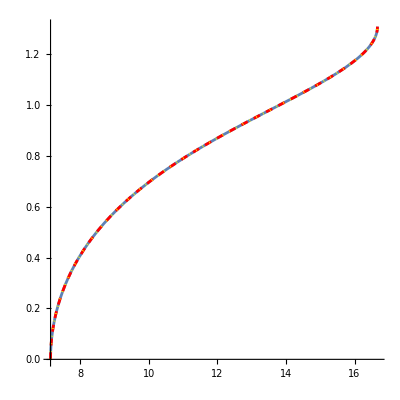

```mathematica
(*The r(λ) inverse*)
rλ[pi_,ei_,spi_,λ_] := (r3(r1 - r2)JacobiSN[(√((1 - ℰ^2)r2(r1-r3)))/2 λ,((r1-r2)r3)/((r1-r3)r2)]^2-r2(r1 -r3))/((r1-r2)JacobiSN[(√((1 - ℰ^2)r2(r1-r3)))/2 λ,((r1-r2)r3)/((r1-r3)r2)]^2 -(r1 - r3))/.Subs/.{p->pi,e->ei,sp->spi};
(*Expression in terms of angle coordinate q^r*)
rqr[pi_,ei_,spi_,qr_]:=(r3(r1 - r2)JacobiSN[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]^2-r2(r1 -r3))/((r1-r2)JacobiSN[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]^2 -(r1 - r3))/.Subs/.{p->pi,e->ei,sp->spi};
(*Consistency check*)
Show[ParametricPlot[{rλ[10,0.4,0.01,λ],λ},{λ,0,Λr/2/.{p->10,e->0.4,sp->0.01}},AspectRatio->1],ParametricPlot[{r,Nλr[10,0.4,0.01,r]},{r,10/(1+0.4),10/(1-0.4)},PlotStyle->{Red,Dashed}],ParametricPlot[{rqr[10,0.4,0.01,qr],qr Λr/(2π)/.{p->10,e->0.4,sp->0.01}},{qr,0,π},PlotStyle->{Yellow,Dotted}]]//Quiet
```

### The t integrals

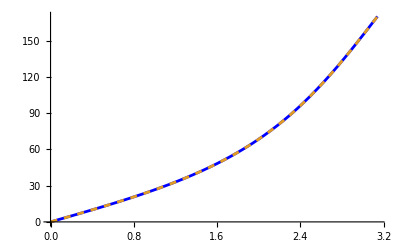

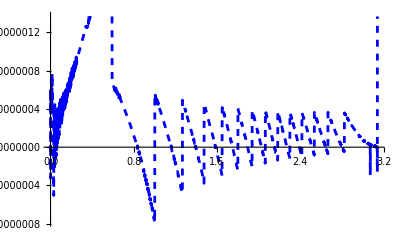

```mathematica
tintegr = (r^2 utint)/(√Rfunc)/.fhRule/.DeTrRule/.Subs;
Nt[pi_,ei_,spi_,rf_] := NIntegrate[tintegr/.{p->pi,e->ei,sp->spi},{r,pi/(1+ei),rf}];
(*Subscript[T̃, r](χ):*)
Ttr[pi_,ei_,spi_,χ_]:= (ℰ/(√((1 - ℰ^2)r2(r1 - r3)))((2M(r1 - r3)(r2-r3) + r3(r3(r2 + r3) - r1(r2 - r3)) -2 𝒥/ℰ M sp)/(r3 - 2M)EllipticF[χ,((r1-r2)r3)/((r1-r3)r2)] + (r1  + r2 + r3 +4M)(r2 -r3) EllipticPi[(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)] + r2(r1-r3)EllipticE[χ,((r1-r2)r3)/((r1-r3)r2)] - (2 M(r2-r3)(8 M^2 - 𝒥/ℰ sp))/((r2 - 2M)(r3 - 2 M))EllipticPi[(r1-r2)/(r1-r3) (r3-2M)/(r2 - 2M),χ,((r1-r2)r3)/((r1-r3)r2)] -((r1-r2) √(r2 (r1-r3) (r2 (r1-r3)-(r1-r2) r3 Sin[χ]^2)) Sin[2 χ])/(r1+r2-2 r3+(r1-r2) Cos[2 χ])))/.Subs/.{p->pi,e->ei,sp->spi};
spf = 1;
Plot[{Ttr[10,0.4,spf,JacobiAmplitude[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]]/.Subs/.{p->10,e->0.4,sp->spf},Nt[10,0.4,spf,rqr[10,0.4,spf,qr]]},{qr,0,π},PlotStyle->{Blue,Dashed}]//Quiet
Plot[(Ttr[10,0.4,spf,JacobiAmplitude[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]]/.Subs/.{p->10,e->0.4,sp->spf})-Nt[10,0.4,spf,rqr[10,0.4,spf,qr]],{qr,0,π},PlotStyle->{Blue,Dashed}]//Quiet
```

```mathematica
ΥtOS=ΥrOS/(2π)(ℰ/(√((1 - ℰ^2)r2(r1 - r3)))((2M(r1 - r3)(r2-r3) + r3(r3(r2 + r3) - r1(r2 - r3)) + 𝒥/ℰ M sp)/(r3 - 2M)EllipticF[χ,((r1-r2)r3)/((r1-r3)r2)] + (r1  + r2 + r3 +4M)(r2 -r3) EllipticPi[(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)] + r2(r1-r3)EllipticE[χ,((r1-r2)r3)/((r1-r3)r2)] - (M(r2-r3)(16 M^2 - 𝒥/ℰ sp))/((r2 - 2M)(r3 - 2 M))EllipticPi[(r1-r2)/(r1-r3) (r3-2M)/(r2 - 2M),χ,((r1-r2)r3)/((r1-r3)r2)] -((r1-r2) √(r2 (r1-r3) (r2 (r1-r3)-(r1-r2) r3 Sin[χ]^2)) Sin[2 χ])/(r1+r2-2 r3+(r1-r2) Cos[2 χ])))/.{χ->π} //FullSimplify;
Υt[pi_,ei_,spi_] := ΥtOS/.Subs/.{p->pi,e->ei,sp->spi};
```

### The φ integrals

(√(p^2/(-3-e^2+p)+(√p (-3 (3+e^2)+2 p) √(-4 (-1+e^2)-4 p+p^2) sp)/((-3-e^2+p)^2))-sp √((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))-((-1+e^2)^2 √(p (-4 (-1+e^2)-4 p+p^2)) sp)/(p^2 (-3-e^2+p)^2)))/(√((p/(1-e)-r) r (-p/(1+e)+r) (-(2 p)/(-4+p)+r+(2 √((-4 e^2+(-2+p)^2) p) sp)/(-4+p)^2) (1-(-4 e^2+(-2+p)^2)/(p (-3-e^2+p))+((-1+e^2)^2 √(p (-4 (-1+e^2)-4 p+p^2)) sp)/(p^2 (-3-e^2+p)^2))))

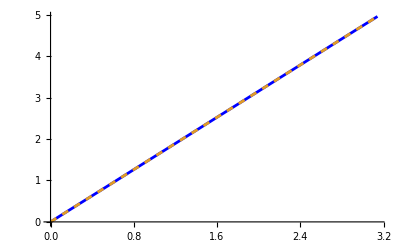

```mathematica
φintegr = (r^2 uφint)/(√Rfunc)/.fhRule/.DeTrRule/.Subs
Nφ[pi_,ei_,spi_,rf_] := NIntegrate[φintegr /.{p->pi,e->ei,sp->spi},{r,pi/(1+ei),rf}];
(*Subscript[T̃, r](χ):*)
Φtr[pi_,ei_,spi_,χ_]:=  2(𝒥 - sp ℰ) EllipticF[χ,((r1-r2)r3)/((r1-r3)r2)]/(√((1 - ℰ^2)r2(r1-r3)))/.Subs/.{p->pi,e->ei,sp->spi};
Plot[{Φtr[10,0.4,0.05,JacobiAmplitude[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]]/.Subs/.{p->10,e->0.4,sp->0.05},Nφ[10,0.4,0.05,rqr[10,0.4,0.05,qr]]},{qr,0,π},PlotStyle->{Blue,Dashed}]//Quiet
```

```mathematica
ΥφOS=(𝒥 - sp ℰ)
Υφ[pi_,ei_,spi_]:=ΥφOS/.Subs/.{p->pi,e->ei,sp->spi};
```

-sp ℰ+𝒥

### The ψ integrals

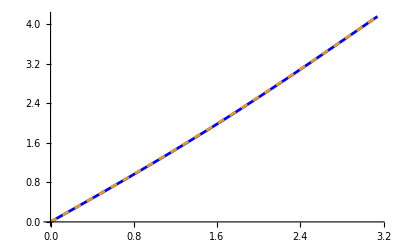

```mathematica
ψintegr = (r^2 ψdot)/(√Rfunc)/.fhRule/.DeTrRule/.Subs/.{sp->0};
Nψ[pi_,ei_,spi_,rf_] := NIntegrate[ψintegr /.{p->pi,e->ei,sp->spi},{r,pi/(1+ei),rf}];
Ψtr[pi_,ei_,spi_,χ_]:=  ((2 ℰ 𝒥)/(√((1 - ℰ^2)(r1 - r3)r2)(𝒥^2 + r3^2))(r3^2 EllipticF[χ,((r1-r2)r3)/((r1-r3)r2)] + (𝒥^2(r2^2 - r3^2))/(𝒥^2 + r2^2)Re[EllipticPi[(r3 - I 𝒥)/(r2 - I 𝒥)(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)]] - (𝒥(r2-r3)(𝒥^2 - r2 r3))/(𝒥^2 + r2^2)Im[EllipticPi[(r3 - I 𝒥)/(r2 - I 𝒥)(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)]]) )/.Subs/.{p->pi,e->ei,sp->spi};
Plot[{Ψtr[10,0.4,0.05,JacobiAmplitude[EllipticK[((r1-r2)r3)/((r1-r3)r2)]/π qr,((r1-r2)r3)/((r1-r3)r2)]]/.Subs/.{p->10,e->0.4,sp->0.05},Nψ[10,0.4,0.05,rqr[10,0.4,0.05,qr]]},{qr,0,π},PlotStyle->{Blue,Dashed}]//Quiet
```

```mathematica
ΥψOS = ΥrOS/(2π)((2 ℰ 𝒥)/(√((1 - ℰ^2)(r1 - r3)r2)(𝒥^2 + r3^2))(r3^2 EllipticF[χ,((r1-r2)r3)/((r1-r3)r2)] + (𝒥^2(r2^2 - r3^2))/(𝒥^2 + r2^2)Re[EllipticPi[(r3 - I 𝒥)/(r2 - I 𝒥)(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)]] - (𝒥(r2-r3)(𝒥^2 - r2 r3))/(𝒥^2 + r2^2)Im[EllipticPi[(r3 - I 𝒥)/(r2 - I 𝒥)(r1-r2)/(r1-r3),χ,((r1-r2)r3)/((r1-r3)r2)]]) )/.{χ->π,sp->0}//FullSimplify
Υψ[pi_,ei_]:=ΥψOS/.Subs/.{p->pi,e->ei,sp->0};
```

(ℰ 𝒥 (r3^2+((r2-r3) 𝒥 ((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),((r1-r2) r3)/(r2 (r1-r3))]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),((r1-r2) r3)/(r2 (r1-r3))]]))/((r2^2+𝒥^2) EllipticK[((r1-r2) r3)/(r2 (r1-r3))])))/(r3^2+𝒥^2)

```mathematica
Υψ0 = Υψ[p,e]//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//FunctionExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//ExpandAll//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

-((-1+e) (6+2 e-p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]+√(-3-e^2+p) (4 EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]))/(√(((-4 e^2+(-2+p)^2) (-3-e^2+p))/p) EllipticK[(4 e)/(-6+2 e+p)])

### Expansion of Mino frequencies in s_(||)

```mathematica
(*First the Mino frequencies*)
```

```mathematica
Υr0 =  Υr[p,e,0]//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
δΥr = (D[Υr[p,e,sp],sp]/.{sp->0})//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

(√(-(p (-6+2 e+p))/(3+e^2-p)) π)/(2 EllipticK[(4 e)/(-6+2 e+p)])

(√((-4 e^2+(-2+p)^2) (-6+2 e+p) (-3-e^2+p)) π ((3+e^2-p) EllipticE[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticK[(4 e)/(-6+2 e+p)]))/(4 (6+2 e-p) (3+e^2-p)^2 EllipticK[(4 e)/(-6+2 e+p)]^2)

```mathematica
Υt0 = Υt[p,e,0]//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//FunctionExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
δΥt = (D[Υt[p,e,sp],sp]/.{sp->0})//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

(√(((-4 e^2+(-2+p)^2) p)/(-3-e^2+p)) (-(p (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p))+(p (36+2 e^2 (-2+p)+(-14+p) p) EllipticK[(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)+2 (6+2 e-p) (((-8+e^2 (8-3 p)+(-1+p) p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)+EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]/(-2-2 e+p))))/(2 EllipticK[(4 e)/(-6+2 e+p)])

((4 (1+e) (3+e^2-p) (-4+p)^2 p (-2-2 e+p)^2 (-6+2 e+p) (-2+2 e+p) EllipticE[(4 e)/(-6+2 e+p)]^2)/(6+2 e-p)-4 (-4+p) (-2-2 e+p) EllipticE[(4 e)/(-6+2 e+p)] ((1+e) p (-6+2 e+p) (-28+e^4 (4+p)-2 e^2 (-3+p) (4+p)+p (33+2 (-7+p) p)) EllipticK[(4 e)/(-6+2 e+p)]+2 (3+e^2-p) (-2+2 e+p) ((2+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+(-1+e) (1+e)^2 (-4+p)^2 EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))+EllipticK[(4 e)/(-6+2 e+p)] (-((1+e) (2+2 e-p) p (-3072+48 e^6 p+e^4 p (112+p (32+3 (-12+p) p))+p (4560+p (-2848+p (892+7 (-19+p) p)))+e^2 (3072+p (-2672+p (1024+p (-280+(50-3 p) p))))) EllipticK[(4 e)/(-6+2 e+p)])+(6+2 e-p) (8 (2+2 e-p) (-128+3 e^6 p^2+e^4 (-128+p (80+3 p-6 p^2))-p (-144+p (55+p (2+(-6+p) p)))+e^2 (256+p (-224+p (113-40 p+6 p^2)))) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+(-1+e) (1+e)^2 (-4+p)^3 (32-p (32+(-11+p) p)+e^2 (-32+p^2)) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])))/(16 (-1+e) (1+e)^2 (4-p)^3 (-2-2 e+p) (-3-e^2+p)^(3/2) EllipticK[(4 e)/(-6+2 e+p)]^2)

```mathematica
Υφ0 = Υφ[p,e,0]//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//FunctionExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
δΥφ = (D[Υφ[p,e,sp],sp]/.{sp->0})//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

p/(√(-3-e^2+p))

-((3+e^2) √(-4+(4-4 e^2)/p+p))/(2 (-3-e^2+p)^(3/2))

### Expansion of orbital evolution in s_(||)

#### Expansion of r

```mathematica
r0 = rqr[p,e,0,qr]//FunctionExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
δr =( D[rqr[p,e,sp,qr],sp]/.{sp->0})//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&//PowerExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
```

(p (-6+2 e+p-4 e JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]^2))/((1+e) (-6+2 e+p)-2 e (-4+p) JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]^2)

-((2 e √((-4 e^2+(-2+p)^2) p) JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] (JacobiCN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] JacobiDN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] ((-6+2 e+p) qr EllipticE[(4 e)/(-6+2 e+p)]-(-6+2 e+p) π JacobiEpsilon[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]+4 e π JacobiCD[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)])+4 e π JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] (-1+JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]^2)))/(π ((1+e) (-6+2 e+p)-2 e (-4+p) JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]^2)^2))

```mathematica
(*Expression in paper:*)
rqr0 /.{JacobiCN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] -> Cos[χ0],JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> Sin[χ0],JacobiDN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> √(1-Subscript[k, 0]^2 Sin[χ0]^2) ,JacobiEpsilon[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> Ε[χ0,k],EllipticE[(4 e)/(-6+2 e+p)]->Ε[k]} 
δrqr/.{JacobiCN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] -> Cos[χ0],JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> Sin[χ0],JacobiDN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> √(1-Subscript[k, 0]^2 Sin[χ0]^2) ,JacobiEpsilon[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]->Ε[χ0,k],EllipticE[(4 e)/(-6+2 e+p)]->Ε[k]} //Simplify(*/.{JacobiCN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)] -> cn[Subscript[λ, r],Subscript[k, 0]],JacobiSN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> sn[Subscript[λ, r],Subscript[k, 0]],JacobiDN[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> dn[Subscript[λ, r],Subscript[k, 0]] ,JacobiEpsilon[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]-> ε[Subscript[λ, r],Subscript[k, 0]],EllipticE[(4 e)/(-6+2 e+p)]->Ε[k]} *)
```

(p (-6+2 e+p-4 e Sin[χ0]^2))/((1+e) (-6+2 e+p)-2 e (-4+p) Sin[χ0]^2)

(e √((-4 e^2+(-2+p)^2) p) (-6+2 e+p) Sin[2 χ0] √(1-Sin[χ0]^2 k_0^2) (-qr Ε[k]+π Ε[χ0,k]))/(π (-6+2 e^2+p+e (-4+p) Cos[2 χ0])^2)

```mathematica
(*Non-expanded expressions*)
```

#### Expansion of t

```mathematica
χ0qr = JacobiAmplitude[qr/π EllipticK[((r1-r2)r3)/((r1-r3)r2)],((r1-r2)r3)/((r1-r3)r2)]/.Subs/.sp->0//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
δχ =Coefficient[ Series[JacobiAmplitude[qr/π EllipticK[((r1-r2)r3)/((r1-r3)r2)],((r1-r2)r3)/((r1-r3)r2)]/.Subs,{sp,0,1}],sp]/.{JacobiCN[_,_] -> Cos[χ0], JacobiSN[_,_]-> Sin[χ0], JacobiDN[_,_]-> √(1-k0^2 Sin[χ0]^2) ,JacobiEpsilon[_,_]->EllipticE[χ0,k0],EllipticE[_]->EllipticE[k0]}/.{k0->(4 e)/(-6+2 e+p)} //FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
(*Consistency check, δχ does not change value at χ=π:*)
δχ/.{χ0->π,qr->2π}//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
```

JacobiAmplitude[(qr EllipticK[(4 e)/(-6+2 e+p)])/π,(4 e)/(-6+2 e+p)]

(√((-4 e^2+(-2+p)^2) p) (-qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]+π √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)]-2 e π Sin[2 χ0]))/(2 p (-6-2 e+p) (-6+2 e+p) π)

0

```mathematica
t0 = (qt+Ttr[p,e,sp,χ0+sp δχ] - Ttr[p,e,sp,π] qr/(2π))/.{sp->0}//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&//PowerExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
```

qt-(√((-4 e^2+(-2+p)^2)/(-6+2 e+p)) qr (-(p (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))/π+√((-4 e^2+(-2+p)^2)/(-6+2 e+p)) (-(p (-6+2 e+p) EllipticE[χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticF[χ0,(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/(2+2 e-p)+(e p √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) Sin[2 χ0])/((-1+e^2) (-6+2 e^2+p+e (-4+p) Cos[2 χ0])))

```mathematica
δt = (D[qt+Ttr[p,e,sp,χ0+sp δχ] - Ttr[p,e,sp,π] qr/(2π),sp]/.{sp->0})//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-(((-1+e) (3+e) (-4 e^2+(-2+p)^2) p qr (-(p (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))/(2 (-(p (-6+2 e+p))/(3+e^2-p))^(3/2) (-3-e^2+p)^(5/2) π))+((-1+e^2)^2 (-3-e^2+p) qr (-(p (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))/(2 (3+e^2-p)^2 √(p (-6+2 e+p)) π)-1/(2 π)√((-4 e^2+(-2+p)^2)/(p^2 (-6+2 e+p))) qr ((4 p √((-4 e^2+(-2+p)^2) p) EllipticE[(4 e)/(-6+2 e+p)])/((1+e) (-4+p)^2)+(p √((-4 e^2+(-2+p)^2) p) (EllipticE[(4 e)/(-6+2 e+p)]-EllipticK[(4 e)/(-6+2 e+p)]))/((-1+e) (1+e) (-4+p))+(p^2 √((-4 e^2+(-2+p)^2) p) (36+2 e^2 (-2+p)-14 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(2 (-1+e^2) (-4+p)^3)-(p^(3/2) (128-144 p-32 p^2+64 p^3-17 p^4+p^5-16 e^4 (-8+5 p)+e^2 (-256-32 p+32 p^2+p^4)) EllipticK[(4 e)/(-6+2 e+p)])/(2 (-1+e^2) √(-4 e^2+(-2+p)^2) (-4+p)^3)+(p √((-4 e^2+(-2+p)^2) p) (36+2 e^2 (-2+p)-14 p+p^2) ((-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)]+(6+2 e-p) EllipticK[(4 e)/(-6+2 e+p)]))/((-1+e) (1+e) (6+2 e-p) (-4+p)^2 (-6+2 e+p))-(4 p √((-4 e^2+(-2+p)^2) p) (-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((1+e) (-4+p)^3)-(8 √((-4 e^2+(-2+p)^2) p) (-8+e^2 (8-3 p)-p+p^2) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^3)-(4 √((-4 e^2+(-2+p)^2) p) (-8+e^2 (8-3 p)-p+p^2) ((1+e) (-6+2 e+p) EllipticK[(4 e)/(-6+2 e+p)]-(-6+2 e^2+3 e (-4+p)+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]))/((-1+e) (1+e)^2 (-4+p)^3 (-6+2 e+p))-(8 (1+e) √((-4 e^2+(-2+p)^2) p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/((-4+p) (-2-2 e+p))+(p^(5/2) (-6-2 e+p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2 √(-4 e^2+(-2+p)^2) (-2-2 e+p))-(p √((-4 e^2+(-2+p)^2) p) (-6-2 e+p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/((-4+p) (-2-2 e+p))+1/(2 (2+2 e-p) (-6+2 e+p))√((-4 e^2+(-2+p)^2) p) ((12+8 e-4 e^2-8 p+p^2) EllipticK[(4 e)/(-6+2 e+p)]+(-12-24 e+4 e^2+8 p-p^2) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))+((-1+e) (3+e) (-4 e^2+(-2+p)^2) p (-(p (-6+2 e+p) EllipticE[χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticF[χ0,(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/(2+2 e-p)+(e p √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) Sin[2 χ0])/((-1+e^2) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))))/(2 (-(p (-6+2 e+p))/(3+e^2-p))^(3/2) (-3-e^2+p)^(5/2))-((-1+e^2)^2 (-3-e^2+p) (-(p (-6+2 e+p) EllipticE[χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(p (36+2 e^2 (-2+p)-14 p+p^2) EllipticF[χ0,(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^2)-(2 (6+2 e-p) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2 (-4+p)^2)-(2 (6+2 e-p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/(2+2 e-p)+(e p √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) Sin[2 χ0])/((-1+e^2) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))))/(2 (3+e^2-p)^2 √(p (-6+2 e+p)))+√((-4 e^2+(-2+p)^2)/(p^2 (-6+2 e+p))) ((2 p √((-4 e^2+(-2+p)^2) p) EllipticE[χ0,(4 e)/(-6+2 e+p)])/((1+e) (-4+p)^2)+(p^2 √((-4 e^2+(-2+p)^2) p) (36+2 e^2 (-2+p)-14 p+p^2) EllipticF[χ0,(4 e)/(-6+2 e+p)])/(4 (-1+e^2) (-4+p)^3)-(p^(3/2) (128-144 p-32 p^2+64 p^3-17 p^4+p^5-16 e^4 (-8+5 p)+e^2 (-256-32 p+32 p^2+p^4)) EllipticF[χ0,(4 e)/(-6+2 e+p)])/(4 (-1+e^2) √(-4 e^2+(-2+p)^2) (-4+p)^3)+(p √((-4 e^2+(-2+p)^2) p) (36+2 e^2 (-2+p)-14 p+p^2) (qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]+π (-6 √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p))+2 e √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p))+p √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p))-√(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0])) EllipticE[χ0,(4 e)/(-6+2 e+p)]+(6+2 e-p) π √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) EllipticF[χ0,(4 e)/(-6+2 e+p)]))/(2 (-1+e) (1+e) (6+2 e-p) (-4+p)^2 π √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])))-(2 p √((-4 e^2+(-2+p)^2) p) (-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)])/((1+e) (-4+p)^3)-(4 √((-4 e^2+(-2+p)^2) p) (-8+e^2 (8-3 p)-p+p^2) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)])/((-1+e^2) (-4+p)^3)-(4 (1+e) √((-4 e^2+(-2+p)^2) p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/((-4+p) (-2-2 e+p))+(p^(5/2) (-6-2 e+p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/(4 √(-4 e^2+(-2+p)^2) (-2-2 e+p))-(p √((-4 e^2+(-2+p)^2) p) (-6-2 e+p) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)])/(2 (-4+p) (-2-2 e+p))+(e p^(3/2) Cos[2 χ0] √(((-4 e^2+(-2+p)^2) (-6+p+2 e Cos[2 χ0]))/(-6+2 e+p)) (qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]-π √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)]+2 e π Sin[2 χ0]))/((-1+e^2) (6+2 e-p) π (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))-(p √((-4 e^2+(-2+p)^2) p) (qr √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]+π ((-6-2 e+p-√((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0])) EllipticE[χ0,(4 e)/(-6+2 e+p)]+(6+2 e-p) EllipticF[χ0,(4 e)/(-6+2 e+p)]+2 e √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) Sin[2 χ0])))/(2 (-1+e) (1+e) (6+2 e-p) (-4+p) π)-1/(4 (2+2 e-p) (-6+2 e+p))(1+e) (1/(1+e)-2/(-4+p)) (-4+p) √((-4 e^2+(-2+p)^2) p) ((4 (2+2 e-p) (-√((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) EllipticE[χ0,(4 e)/(-6+2 e+p)]-(6+2 e-p) √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)]+2 e Sin[2 χ0]))/((-6-2 e+p)^2 √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)))+(4 (2+2 e-p) (-6+2 e+p)^(3/2) (qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]-π √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)]+2 e π Sin[2 χ0]))/((6+2 e-p) π √(-6+p+2 e Cos[2 χ0]) (12-4 e^2-8 p+p^2+8 e Cos[2 χ0]))-(4 (2+2 e-p) (-6+2 e+p) (-12+4 e^2+8 p-p^2-8 e Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)]-(2+2 e-p) (6+2 e-p) (-6+2 e+p) (-12+4 e^2+8 p-p^2-8 e Cos[2 χ0]) EllipticF[χ0,(4 e)/(-6+2 e+p)]+(64 e-(-2-2 e+p)^2 (-6+2 e+p)) (12-4 e^2-8 p+p^2+8 e Cos[2 χ0]) EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),χ0,(4 e)/(-6+2 e+p)]+32 e (2+2 e-p) √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) Sin[2 χ0])/((-6-2 e+p)^2 (12-4 e^2-8 p+p^2+8 e Cos[2 χ0])))-((1/(1+e)-2/(-4+p)) √((-4 e^2+(-2+p)^2) p) (4+(1/(1-e)+1/(1+e)+2/(-4+p)) p) (1/(√((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)))2 (1+e) (-√((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) EllipticE[χ0,(4 e)/(-6+2 e+p)]-(6+2 e-p) √((-6+p+2 e Cos[2 χ0])/(-6+2 e+p)) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)]+2 e Sin[2 χ0])-((1+e) (6+2 e-p) (-6+2 e+p)^(3/2) (qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)]-π √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)]+2 e π Sin[2 χ0]))/(π √(-6+p+2 e Cos[2 χ0]) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))+(2 (1-e) (-((1+e) (-4+p) (-6+2 e+p) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)])-(1+e) (6+2 e-p) (-6+2 e+p) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]) EllipticF[χ0,(4 e)/(-6+2 e+p)]+2 (-6+2 e^3+e^2 (-2+p)+p-e (26-10 p+p^2)) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),χ0,(4 e)/(-6+2 e+p)]+e (1+e) (-4+p)^2 √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) Sin[2 χ0]))/((-1+e) (-4+p) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))))/(2 (-6-2 e+p)^2 (-6+2 e+p))+(e p √((-4 e^2+(-2+p)^2) p) Sin[2 χ0] (-e (-4+p) qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)] Sin[2 χ0]+π (-72+24 e+20 e^2+24 p-10 e p-3 e^2 p-2 p^2+e p^2-e (-48+8 e^2-2 e (-4+p)+14 p-p^2) Cos[2 χ0]-4 e^2 Cos[4 χ0]+e^2 p Cos[4 χ0]+e (-4+p) √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)] Sin[2 χ0])))/((-1+e) (1+e) (6+2 e-p) (-4+p) π √((-6+2 e+p) (-6+p+2 e Cos[2 χ0])) (-6+2 e^2+p+e (-4+p) Cos[2 χ0]))-(e p^(3/2) √(((-4 e^2+(-2+p)^2) (-6+p+2 e Cos[2 χ0]))/(-6+2 e+p)) Sin[2 χ0] (-e (-4+p)^2 qr √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[(4 e)/(-6+2 e+p)] Sin[2 χ0]+π (-72+64 e^2-8 e^4+24 p-16 e^2 p-2 p^2+e^2 p^2+e^2 (-4+p)^2 Cos[4 χ0]+e (-4+p)^2 √(-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]) EllipticE[χ0,(4 e)/(-6+2 e+p)] Sin[2 χ0])))/((-1+e^2) (6+2 e-p) (-4+p) π (-6+2 e^2+p+e (-4+p) Cos[2 χ0])^2))

```mathematica
(*This cell will take a long time to evaluate since δt is a very complicated expression*)
δt = δt//PowerExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,qr ∈Reals,χ0∈Reals}]&
```

```mathematica
avg = Coefficient[Series[ Ttr[p,e,sp,π],{sp,0,1}],sp]//FunctionExpand //FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//FullSimplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

1/((-4+p)^3 √(p (-6+2 e+p)))p (((-4+p) p (-44+12 e^2+(20-3 p) p) EllipticE[(4 e)/(-6+2 e+p)])/(-6-2 e+p)+(-128+p (148+12 e^2+p (-44+3 p))) EllipticK[(4 e)/(-6+2 e+p)]-(6 (6+2 e-p) (3+e^2-p) p EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/(1+e))

#### Expansion of φ

```mathematica
φ0 = (qφ+Φtr[p,e,sp,χ0+sp δχ] - Φtr[p,e,sp,π] qr/(2π))/.{sp->0}//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

(√(p (-6+2 e+p)) π qφ+2 p π EllipticF[χ0,(4 e)/(-6+2 e+p)]-2 p qr EllipticK[(4 e)/(-6+2 e+p)])/(√(p (-6+2 e+p)) π)

```mathematica
δφ =( D[qφ+Φtr[p,e,sp,χ0+sp δχ] - Φtr[p,e,sp,π] qr/(2π),sp]/.{sp->0})//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,χ0 ∈Reals,qr∈Reals}]&//PowerExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0,χ0 ∈Reals,qr∈Reals}]&
```

1/((6+2 e-p) p (-6+2 e+p)^(3/2) π √(-6+p+2 e Cos[2 χ0]))ⅈ √(4 e^2-(-2+p)^2) (p qr (-6 √(-6+p+2 e Cos[2 χ0])+2 e √(-6+p+2 e Cos[2 χ0])+p √(-6+p+2 e Cos[2 χ0])-√((-6+2 e+p) (-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]))) EllipticE[(4 e)/(-6+2 e+p)]-p π (-6 √(-6+p+2 e Cos[2 χ0])+2 e √(-6+p+2 e Cos[2 χ0])+p √(-6+p+2 e Cos[2 χ0])-√((-6+2 e+p) (-4 e^2+4 e (-6+p)+(-6+p)^2+8 e^2 Cos[2 χ0]))) EllipticE[χ0,(4 e)/(-6+2 e+p)]+(-4 e^2+(-6+p)^2) √(-6+p+2 e Cos[2 χ0]) (π EllipticF[χ0,(4 e)/(-6+2 e+p)]-qr EllipticK[(4 e)/(-6+2 e+p)]))

#### Non-expansion of ψ, spin vector, δϑ

```mathematica
(*Only the leading-order has been solved for*)
ψ0 = (qψ + Ψtr[p,e,0,χ0] - Ψtr[p,e,0,π] qr/(2π))/.{sp->0}//FunctionExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&//PowerExpand//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
```

1/((4 e^2-(-2+p)^2) (-2+2 e+p) π)√((-3-e^2+p)/(-6+2 e+p)) ((2+2 e-p) (-2+2 e+p)^2 √((-6+2 e+p)/(-3-e^2+p)) π qψ+2 √(-4 e^2+(-2+p)^2) qr (-4 (-2+2 e+p) EllipticK[(4 e)/(-6+2 e+p)]-((-1+e) (6+2 e-p) (-2+2 e+p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]])/(√(-3-e^2+p))+(4 (1+e)^2-(-4+p)^2) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]])-2 √(-4 e^2+(-2+p)^2) π (-4 (-2+2 e+p) EllipticF[χ0,(4 e)/(-6+2 e+p)]-((-1+e) (6+2 e-p) (-2+2 e+p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),χ0,(4 e)/(-6+2 e+p)]])/(√(-3-e^2+p))+(4 (1+e)^2-(-4+p)^2) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),χ0,(4 e)/(-6+2 e+p)]]))

```mathematica
(*This allows to express the spin vector parametrized by the q angles*)
SvecSol/.fhRule/.DeTrRule/.(Subs/.{sp->0})//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
Sv0 = %/.{r->r0,ψ->ψ0} //Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&;
```

{√(s^2-sp^2) ((r Cos[ψ])/((-2+r) √(((-3-e^2+p) (p^2-(3+e^2) r^2+p r^2))/((-4 e^2+(-2+p)^2) p)))+(r √(-((p (-2+r)-4 r) (p^2-2 p r-(-1+e^2) r^2))/(p (-3-e^2+p) (-2+r) r^2)) Sin[ψ])/(√(((-2+r) (p^2/(-3-e^2+p)+r^2))/r))),(√(p^2/(-3-e^2+p)+r^2) √(s^2-sp^2) Cos[ψ])/r^2,(√(s^2-sp^2) (√((p (p (-2+r)-4 r) (p^2-2 p r-(-1+e^2) r^2))/((3+e^2-p) r (p^2-(3+e^2) r^2+p r^2))) Cos[ψ]+(r^2 Sin[ψ])/(√((p (p^2-(3+e^2) r^2+p r^2))/(-4 e^2+(-2+p)^2)))))/r,sp/r}

```mathematica
((*Also we get δθ at leading order*)
√((s-sp) (s+sp) (𝒥^2+rt[τ]^2)) Sin[ψ])/(𝒥 rt[τ])/.DeTrRule/.(Subs/.{sp->0})//Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&
δϑ = %/.{r->r0,ψ->ψ0} //Simplify[#,{p>0,0<e<1,-6+2 e+p>0}]&;
```

(√((p^2-(3+e^2) r^2+p r^2) (s-sp) (s+sp)) Sin[ψ])/(p r)

## Save outputs

```mathematica
OutputPath=NotebookDirectory[]<>"SchwarzschildSpinExact.mx";
(*Back up in case you are overwriting a previous run:*)
If[FileExistsQ[OutputPath],
BackupPath = NotebookDirectory[]<>"SchwarzschildSpinExact_Backup.mx";
DeleteFile[BackupPath];
CopyFile[OutputPath,BackupPath];
DeleteFile[OutputPath];
Print["Output file existed, backup of old file copied into "<>BackupPath],
Print["No old file existed, proceeding."]
];
(*List of variables to export:*)
VarList = {Υt0,Υr0,Υφ0,Υψ0,δΥt,δΥr,δΥφ,t0,r0,φ0,ψ0,χ0qr,Sv0,δt,δr,δφ,δϑ};
DumpSave[OutputPath,VarList];
```

Output file existed, backup of old file copied into /Users/vojtechwitzany/Documents/GitHub/Exact-Solution-Spinning-particle-Schwarzschild/SchwarzschildSpinExact_Backup.mx

## Example plots

```mathematica
(*Here you can find some example plots as well as a practical example of the application of the formulas in this notebook*)
PlotCyc = 10;
pp = 7; ep =0.3; spp = 0; smp = 0.3;
```

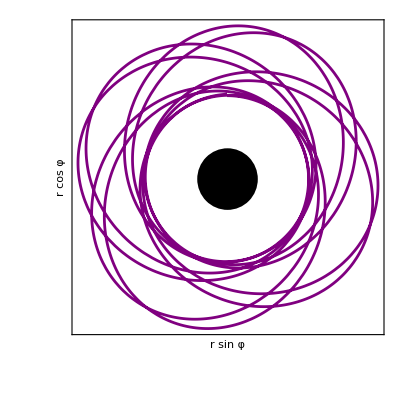

/Users/vojtechwitzany/Documents/GitHub/Exact-Solution-Spinning-particle-Schwarzschild/SpSchwBirdsEye.pdf

```mathematica
BirdsEye = Show[ParametricPlot[({r Sin[φ],r Cos[φ]}/.{t->t0+sp δt,r->r0+sp δr,φ -> φ0 + sp δφ,ϑ->π/2+δϑ}/.{χ0->χ0qr}/.{qr->(Υr0+δΥr) λ,qφ -> (Υφ0+δΥφ) λ,qψ->Υψ0 λ}/.{p->pp,e->ep,s->smp,sp->spp}),{λ,0,PlotCyc (2π)/(Υφ0+δΥφ)/.{p->pp,e->ep,s->smp,sp->spp}},PlotStyle->Purple,Axes->False,Frame->True,FrameLabel->{"r sin φ","r cos φ","",""},FrameTicks->None,LabelStyle->{FontSize->20,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True}],Graphics[{Black,Disk[{0,0},2]}]]
Export[NotebookDirectory[]<>"SpSchwBirdsEye.pdf",BirdsEye]
```

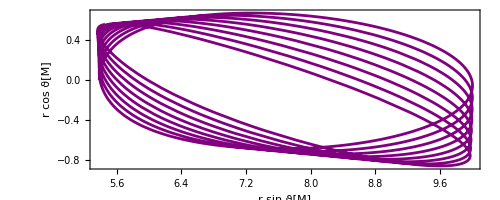

/Users/vojtechwitzany/Documents/GitHub/Exact-Solution-Spinning-particle-Schwarzschild/SpSchwMeridional.pdf

```mathematica
Meridional = Show[ParametricPlot[({r Sin[ϑ],r Cos[ϑ]}/.{t->t0+sp δt,r->r0+sp δr,φ -> φ0 + sp δφ,ϑ->π/2+δϑ}/.{χ0->χ0qr}/.{qr->(Υr0+δΥr) λ,qφ -> (Υφ0+δΥφ) λ,qψ->Υψ0 λ}/.{p->pp,e->ep,s->smp,sp->spp}),{λ,0,PlotCyc (2π)/(Υφ0+δΥφ)/.{p->pp,e->ep,s->smp,sp->spp}},PlotStyle->Purple,Ticks->None,Axes->False,Frame->True,FrameLabel->{"r sin ϑ[M]","r cos ϑ[M]","",""},FrameTicks->{{-0.5,0,0.5},{5,10},None,None},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True}],Graphics[{Black,Disk[{0,0},2]}]]
Export[NotebookDirectory[]<>"SpSchwMeridional.pdf",Meridional]
```

```mathematica
GenericView = Show[ParametricPlot3D[({r Cos[ϑ],r Sin[φ]Sin[ϑ],r Cos[φ0]Sin[ϑ]}/.{t->t0+sp δt,r->r0+sp δr,φ -> φ0 + sp δφ,ϑ->π/2+δϑ}/.{χ0->χ0qr}/.{qr->(Υr0+δΥr) λ,qφ -> (Υφ0+δΥφ) λ,qψ->Υψ0 λ}/.{p->pp,e->ep,s->smp,sp->spp}),{λ,0,PlotCyc (2π)/(Υφ0+δΥφ)/.{p->pp,e->ep,s->smp,sp->spp}},PlotRange->{{-2,2},Automatic,Automatic},Boxed->False,Axes->False,Lighting->"ThreePoint",MaxRecursion->6,PlotStyle->Purple,Method->{"ShrinkWrap"->True}],Graphics3D[{MaterialShading[<|"BaseColor"->GrayLevel[0.4],"MetallicCoefficient"->1,"RoughnessCoefficient"->0.65|>],Sphere[{0,0,0},2]}]]
Export[NotebookDirectory[]<>"SpSchwGeneric.pdf",GenericView]
```

-Graphics3D-

/Users/vojtechwitzany/Documents/GitHub/Exact-Solution-Spinning-particle-Schwarzschild/SpSchwGeneric.pdf

## Sandbox